```mathematica
1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)+√((-1-1 C1/C2(1+R1/R2))^2-(4R1 C1)/(R2 C2)))/.R1->30000/.R2->10000/.C1->10^-6/.C2->2 10^-6
```

50/3 (-3+√3)

```mathematica
(-1-1 C1/C2(1+R1/R2))^2-(4R1 C1)/(R2 C2)//Expand//FullSimplify
```

(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)/(C2^2 R2^2)

```mathematica
Solve[{A+B==u20,u10/(R1 C2)+U20(1/(R1 C2)+1/(R2 C2))==-A λ1-B λ2},{A,B}]//FullSimplify
```

{{A→-(R2 u10+R1 U20+R2 U20+C2 R1 R2 u20 λ2)/(C2 R1 R2 λ1-C2 R1 R2 λ2),B→(R2 u10+R1 U20+R2 U20+C2 R1 R2 u20 λ1)/(C2 R1 R2 λ1-C2 R1 R2 λ2)}}

```mathematica
1/(2R2)(-A^2/λ1-B^2/λ2-(4A B)/(λ1+λ2))/.A->1/(λ2-λ1)(u20 λ2+u10/(R1 C2)+u20/C2(1/R1+1/R2))/.B->-1/(λ2-λ1)(u20 λ1+u10/(R1 C2)+u20/C2(1/R1+1/R2))/.λ1->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)-√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.λ2->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)+√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.R1->30000/.R2->10000/.C1->10^-6/.C2->2 10^-6/.u10->200/.u20->100//Simplify
```

```mathematica
1/200
```

```mathematica
%126/.λ1->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)-√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.λ2->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)+√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.R1->30000/.R2->10000/.C1->10^-6/.C2->2 10^-6/.u10->200/.u20->100//Simplify
```

3/200

```mathematica
DSolveValue[{u1'[t]==-(u1[t]+u2[t])/(R1 C1),u2'[t]==-u2[t]/(R2 C2)-(u1[t]+u2[t])/(R1 C2),u1[0]==u10,u2[0]==u20},{u1[t],u2[t]},t]
```

{(-C1 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R1 u10+C1 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R1 u10-C1 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10+C2 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10+C1 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10-C2 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10+ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2) u10+ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2) u10+2 C2 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20-2 C2 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20)/(2 √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)),(2 C1 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10-2 C1 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u10+C1 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R1 u20-C1 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R1 u20+C1 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20-C2 ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20-C1 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20+C2 ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) R2 u20+ⅇ^(((-C1 R1-C1 R2-C2 R2-√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2) u20+ⅇ^(((-C1 R1-C1 R2-C2 R2+√(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2)) t)/(2 C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2) u20)/(2 √(-4 C1 C2 R1 R2+(C1 R1+C1 R2+C2 R2)^2))}

```mathematica
FullSimplify[%120,C1>0&&C2>0&&R1>0&&R2>0&&u10>0&&u20>0]
```

{(ⅇ^(-((C2 R2+C1 (R1+R2)+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)) t)/(2 C1 C2 R1 R2)) (-C1 R1 u10-C1 R2 u10+C2 R2 u10+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u10+ⅇ^((√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) t)/(C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u10+2 C2 R2 u20+ⅇ^((√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) t)/(C1 C2 R1 R2)) (C1 (R1+R2) u10-C2 R2 (u10+2 u20))))/(2 √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)),(ⅇ^(-((C2 R2+C1 (R1+R2)+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)) t)/(2 C1 C2 R1 R2)) (2 C1 R2 u10+C1 R1 u20+C1 R2 u20-C2 R2 u20+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u20+ⅇ^((√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) t)/(C1 C2 R1 R2)) √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u20+ⅇ^((√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) t)/(C1 C2 R1 R2)) (C2 R2 u20-C1 (2 R2 u10+(R1+R2) u20))))/(2 √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2))}

```mathematica
Integrate[1/R2(ⅇ^(λ1 t) A+ⅇ^(λ2 t) B)^2,{t,0,∞}]
```

ConditionalExpression[(-A^2/(2 λ1)-B^2/(2 λ2)-(2 A B)/(λ1+λ2))/R2,Re[λ2]<0&&Re[λ1]<0]

```mathematica
%122/.R1->30000/.R2->10000/.C1->10^-6/.C2->2 10^-6/.u10->200/.u20->100
```

1/200

```mathematica
DSolveValue[{R1 C1 u2''[t]+u2'[t](1+C1/C2(1+R1/R2))+u2[t]/(R2 C2)==0,u2[0]==u20,u2'[0]==-(u10+u20)/(R1 C2)-u20/(R2 C2)},u2[t],t]
```

(2 C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)-√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u10-2 C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)+√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u10+C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)-√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R1 u20-C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)+√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R1 u20+C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)-√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u20-C2 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)-√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u20-C1 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)+√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u20+C2 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)+√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R2 u20+C1 C2 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)-√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R1 R2 √(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2)) u20+C1 C2 ⅇ^(1/2 (-1/(C1 R1)-1/(C2 R1)-1/(C2 R2)+√(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2))) t) R1 R2 √(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2)) u20)/(2 C1 C2 R1 R2 √(-4/(C1 C2 R1 R2)+(C1 R1+C1 R2+C2 R2)^2/(C1^2 C2^2 R1^2 R2^2)))

```mathematica
FullSimplify[%147,C1>0&&C2>0&&R1>0&&R2>0&&u10>0&&u20>0]
```

(ⅇ^(-((C2 R2+C1 (R1+R2)+√(C1^2 R1^2+2 C1 (C1-C2) R1 R2+(C1+C2)^2 R2^2)) t)/(2 C1 C2 R1 R2)) (2 C1 R2 u10+C1 R1 u20+C1 R2 u20-C2 R2 u20+√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) u20+ⅇ^((√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) t)/(C1 C2 R1 R2)) √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) u20+ⅇ^((√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) t)/(C1 C2 R1 R2)) (C2 R2 u20-C1 (2 R2 u10+(R1+R2) u20))))/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2))

```mathematica
{1/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2))(2 C1 R2 u10+C1 R1 u20+C1 R2 u20-C2 R2 u20+√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) u20),1/(λ2-λ1)(u20 λ2+u10/(R1 C2)+u20/C2(1/R1+1/R2))}/.λ1->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)-√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.λ2->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)+√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))//Expand//Simplify
```

{((-C2 R2+√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)) u20+C1 (R1 u20+R2 (2 u10+u20)))/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)),(2 C1 R2 u10+C1 R1 u20+C1 R2 u20-C2 R2 u20+C2 R2 √((-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)/(C2^2 R2^2)) u20)/(2 C2 R2 √((-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)/(C2^2 R2^2)))}

```mathematica
FullSimplify[%164,C1>0&&C2>0&&R1>0&&R2>0&&u10>0&&u20>0]
```

{(2 C1 R2 u10+C1 (R1+R2) u20+(-C2 R2+√(C1^2 R1^2+2 C1 (C1-C2) R1 R2+(C1+C2)^2 R2^2)) u20)/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)),(2 C1 R2 u10+C1 R1 u20+C1 R2 u20-C2 R2 u20+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u20)/(2 √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2))}

```mathematica
{(√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2) u20+ (C2 R2 u20-C1 (2 R2 u10+(R1+R2) u20)))/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)),-1/(λ2-λ1)(u20 λ1+u10/(R1 C2)+u20/C2(1/R1+1/R2))}/.λ1->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)-√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))/.λ2->1/(2R1 C1)(-1-1 C1/C2(1+R1/R2)+√((-1-1 C1/C2(1+R1/R2))^2-4(R1 C1)/(R2 C2)))//Expand//Simplify
```

{((C2 R2+√(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)) u20-C1 (R1 u20+R2 (2 u10+u20)))/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)),(-2 C1 R2 u10-C1 R1 u20-C1 R2 u20+C2 R2 u20+C2 R2 √((-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)/(C2^2 R2^2)) u20)/(2 C2 R2 √((-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2)/(C2^2 R2^2)))}

```mathematica
FullSimplify[%168,C1>0&&C2>0&&R1>0&&R2>0&&u10>0&&u20>0]
```

{((C2 R2+√(C1^2 R1^2+2 C1 (C1-C2) R1 R2+(C1+C2)^2 R2^2)) u20-C1 (2 R2 u10+(R1+R2) u20))/(2 √(C2^2 R2^2+2 C1 C2 R2 (-R1+R2)+C1^2 (R1+R2)^2)),(-2 C1 R2 u10-C1 R1 u20-C1 R2 u20+C2 R2 u20+√(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2) u20)/(2 √(-4 C1 C2 R1 R2+(C2 R2+C1 (R1+R2))^2))}

```mathematica
%165[[1]]-%165[[2]]//FullSimplify
```

0

```mathematica
%169[[1]]-%169[[2]]//FullSimplify
```

0

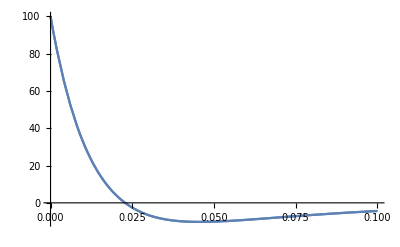

```mathematica
Plot[{%147,%121[[2]]}/.R1->30000/.R2->10000/.C1->10^-6/.C2->2 10^-6/.u10->200/.u20->100,{t,0,0.1},PlotRange->All]
```